# Bistable motif: parameter sampling

## Finding the condition of multistationarity

We consider the following reactions:

K+S⇋KS→K+S_p
K^✶+S⇋K^✶S→K^✶+S_p
S_p→S
K⇋K^✶
KS⇋K^✶S

The species of the system are:

{S,S_p,K,K^✶,KS,K^✶S}

In total, there are 11 reations and 6 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms]
```

-k_2^2 k_5^2 k_7 k_8 k_9-2 k_2 k_3 k_5^2 k_7 k_8 k_9-k_3^2 k_5^2 k_7 k_8 k_9-2 k_2^2 k_5 k_6 k_7 k_8 k_9-4 k_2 k_3 k_5 k_6 k_7 k_8 k_9-2 k_3^2 k_5 k_6 k_7 k_8 k_9-k_2^2 k_6^2 k_7 k_8 k_9-2 k_2 k_3 k_6^2 k_7 k_8 k_9-k_3^2 k_6^2 k_7 k_8 k_9-k_2^2 k_5^2 k_7 k_9^2-2 k_2 k_3 k_5^2 k_7 k_9^2-k_3^2 k_5^2 k_7 k_9^2-2 k_2^2 k_5 k_6 k_7 k_9^2-4 k_2 k_3 k_5 k_6 k_7 k_9^2-2 k_3^2 k_5 k_6 k_7 k_9^2-k_2^2 k_6^2 k_7 k_9^2-2 k_2 k_3 k_6^2 k_7 k_9^2-k_3^2 k_6^2 k_7 k_9^2-2 k_2 k_5^2 k_7 k_8 k_9 k_10-2 k_3 k_5^2 k_7 k_8 k_9 k_10-4 k_2 k_5 k_6 k_7 k_8 k_9 k_10-4 k_3 k_5 k_6 k_7 k_8 k_9 k_10-2 k_2 k_6^2 k_7 k_8 k_9 k_10-2 k_3 k_6^2 k_7 k_8 k_9 k_10-2 k_2 k_5^2 k_7 k_9^2 k_10-2 k_3 k_5^2 k_7 k_9^2 k_10-4 k_2 k_5 k_6 k_7 k_9^2 k_10-4 k_3 k_5 k_6 k_7 k_9^2 k_10-2 k_2 k_6^2 k_7 k_9^2 k_10-2 k_3 k_6^2 k_7 k_9^2 k_10-k_5^2 k_7 k_8 k_9 k_10^2-2 k_5 k_6 k_7 k_8 k_9 k_10^2-k_6^2 k_7 k_8 k_9 k_10^2-k_5^2 k_7 k_9^2 k_10^2-2 k_5 k_6 k_7 k_9^2 k_10^2-k_6^2 k_7 k_9^2 k_10^2-2 k_2^2 k_5 k_7 k_8 k_9 k_11-4 k_2 k_3 k_5 k_7 k_8 k_9 k_11-2 k_3^2 k_5 k_7 k_8 k_9 k_11-2 k_2^2 k_6 k_7 k_8 k_9 k_11-4 k_2 k_3 k_6 k_7 k_8 k_9 k_11-2 k_3^2 k_6 k_7 k_8 k_9 k_11-2 k_2^2 k_5 k_7 k_9^2 k_11-4 k_2 k_3 k_5 k_7 k_9^2 k_11-2 k_3^2 k_5 k_7 k_9^2 k_11-2 k_2^2 k_6 k_7 k_9^2 k_11-4 k_2 k_3 k_6 k_7 k_9^2 k_11-2 k_3^2 k_6 k_7 k_9^2 k_11-2 k_2 k_5 k_7 k_8 k_9 k_10 k_11-2 k_3 k_5 k_7 k_8 k_9 k_10 k_11-2 k_2 k_6 k_7 k_8 k_9 k_10 k_11-2 k_3 k_6 k_7 k_8 k_9 k_10 k_11-2 k_2 k_5 k_7 k_9^2 k_10 k_11-2 k_3 k_5 k_7 k_9^2 k_10 k_11-2 k_2 k_6 k_7 k_9^2 k_10 k_11-2 k_3 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_7 k_8 k_9 k_11^2-2 k_2 k_3 k_7 k_8 k_9 k_11^2-k_3^2 k_7 k_8 k_9 k_11^2-k_2^2 k_7 k_9^2 k_11^2-2 k_2 k_3 k_7 k_9^2 k_11^2-k_3^2 k_7 k_9^2 k_11^2+(-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_1^3+(-k_2^2 k_4 k_5 k_6 k_8^2-2 k_2 k_3 k_4 k_5 k_6 k_8^2-k_3^2 k_4 k_5 k_6 k_8^2-k_2^2 k_4 k_6^2 k_8^2-2 k_2 k_3 k_4 k_6^2 k_8^2-k_3^2 k_4 k_6^2 k_8^2-k_2^2 k_4 k_5 k_7 k_8^2-2 k_2 k_3 k_4 k_5 k_7 k_8^2-k_3^2 k_4 k_5 k_7 k_8^2-k_2^2 k_4 k_6 k_7 k_8^2-2 k_2 k_3 k_4 k_6 k_7 k_8^2-k_3^2 k_4 k_6 k_7 k_8^2-k_1 k_2 k_3 k_5^2 k_8 k_9-k_1 k_3^2 k_5^2 k_8 k_9-2 k_1 k_2 k_3 k_5 k_6 k_8 k_9-2 k_1 k_3^2 k_5 k_6 k_8 k_9-k_2^2 k_4 k_5 k_6 k_8 k_9-2 k_2 k_3 k_4 k_5 k_6 k_8 k_9-k_3^2 k_4 k_5 k_6 k_8 k_9-k_1 k_2 k_3 k_6^2 k_8 k_9-k_1 k_3^2 k_6^2 k_8 k_9-k_2^2 k_4 k_6^2 k_8 k_9-2 k_2 k_3 k_4 k_6^2 k_8 k_9-k_3^2 k_4 k_6^2 k_8 k_9-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_8 k_9-k_1 k_3 k_5^2 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-2 k_1 k_2 k_5 k_6 k_7 k_8 k_9-2 k_1 k_3 k_5 k_6 k_7 k_8 k_9-k_1 k_2 k_6^2 k_7 k_8 k_9-k_1 k_3 k_6^2 k_7 k_8 k_9-k_1 k_2 k_3 k_5^2 k_9^2-k_1 k_3^2 k_5^2 k_9^2-2 k_1 k_2 k_3 k_5 k_6 k_9^2-2 k_1 k_3^2 k_5 k_6 k_9^2-k_1 k_2 k_3 k_6^2 k_9^2-k_1 k_3^2 k_6^2 k_9^2-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-2 k_2 k_4 k_5 k_6 k_8^2 k_10-2 k_3 k_4 k_5 k_6 k_8^2 k_10-2 k_2 k_4 k_6^2 k_8^2 k_10-2 k_3 k_4 k_6^2 k_8^2 k_10-2 k_2 k_4 k_5 k_7 k_8^2 k_10-2 k_3 k_4 k_5 k_7 k_8^2 k_10-2 k_2 k_4 k_6 k_7 k_8^2 k_10-2 k_3 k_4 k_6 k_7 k_8^2 k_10-k_1 k_3 k_5^2 k_8 k_9 k_10-k_1 k_2 k_5 k_6 k_8 k_9 k_10-3 k_1 k_3 k_5 k_6 k_8 k_9 k_10-2 k_2 k_4 k_5 k_6 k_8 k_9 k_10-2 k_3 k_4 k_5 k_6 k_8 k_9 k_10-k_1 k_2 k_6^2 k_8 k_9 k_10-2 k_1 k_3 k_6^2 k_8 k_9 k_10-2 k_2 k_4 k_6^2 k_8 k_9 k_10-2 k_3 k_4 k_6^2 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_8 k_9 k_10-k_1 k_3 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-k_1 k_5^2 k_7 k_8 k_9 k_10-k_1 k_2 k_6 k_7 k_8 k_9 k_10-k_1 k_3 k_6 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-2 k_1 k_5 k_6 k_7 k_8 k_9 k_10-k_1 k_6^2 k_7 k_8 k_9 k_10-k_1 k_3 k_5^2 k_9^2 k_10-k_1 k_2 k_5 k_6 k_9^2 k_10-3 k_1 k_3 k_5 k_6 k_9^2 k_10-k_1 k_2 k_6^2 k_9^2 k_10-2 k_1 k_3 k_6^2 k_9^2 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_4 k_5 k_6 k_8^2 k_10^2-k_4 k_6^2 k_8^2 k_10^2-k_4 k_5 k_7 k_8^2 k_10^2-k_4 k_6 k_7 k_8^2 k_10^2-k_1 k_5 k_6 k_8 k_9 k_10^2-k_4 k_5 k_6 k_8 k_9 k_10^2-k_1 k_6^2 k_8 k_9 k_10^2-k_4 k_6^2 k_8 k_9 k_10^2-k_1 k_5 k_7 k_8 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_1 k_6 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_6 k_9^2 k_10^2-k_1 k_6^2 k_9^2 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2 k_3 k_4 k_5 k_8^2 k_11-k_3^2 k_4 k_5 k_8^2 k_11-k_2^2 k_4 k_6 k_8^2 k_11-3 k_2 k_3 k_4 k_6 k_8^2 k_11-2 k_3^2 k_4 k_6 k_8^2 k_11-k_2^2 k_4 k_7 k_8^2 k_11-2 k_2 k_3 k_4 k_7 k_8^2 k_11-k_3^2 k_4 k_7 k_8^2 k_11-k_2 k_4 k_5 k_7 k_8^2 k_11-k_3 k_4 k_5 k_7 k_8^2 k_11-k_2 k_4 k_6 k_7 k_8^2 k_11-k_3 k_4 k_6 k_7 k_8^2 k_11-2 k_1 k_2 k_3 k_5 k_8 k_9 k_11-2 k_1 k_3^2 k_5 k_8 k_9 k_11-k_2 k_3 k_4 k_5 k_8 k_9 k_11-k_3^2 k_4 k_5 k_8 k_9 k_11-2 k_1 k_2 k_3 k_6 k_8 k_9 k_11-2 k_1 k_3^2 k_6 k_8 k_9 k_11-k_2^2 k_4 k_6 k_8 k_9 k_11-3 k_2 k_3 k_4 k_6 k_8 k_9 k_11-2 k_3^2 k_4 k_6 k_8 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_8 k_9 k_11-2 k_1 k_3 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-2 k_1 k_2 k_6 k_7 k_8 k_9 k_11-2 k_1 k_3 k_6 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_3 k_5 k_9^2 k_11-2 k_1 k_3^2 k_5 k_9^2 k_11-2 k_1 k_2 k_3 k_6 k_9^2 k_11-2 k_1 k_3^2 k_6 k_9^2 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_3 k_4 k_5 k_8^2 k_10 k_11-k_2 k_4 k_6 k_8^2 k_10 k_11-2 k_3 k_4 k_6 k_8^2 k_10 k_11-k_2 k_4 k_7 k_8^2 k_10 k_11-k_3 k_4 k_7 k_8^2 k_10 k_11-k_4 k_5 k_7 k_8^2 k_10 k_11-k_4 k_6 k_7 k_8^2 k_10 k_11-k_1 k_3 k_5 k_8 k_9 k_10 k_11-k_3 k_4 k_5 k_8 k_9 k_10 k_11-k_1 k_2 k_6 k_8 k_9 k_10 k_11-2 k_1 k_3 k_6 k_8 k_9 k_10 k_11-k_2 k_4 k_6 k_8 k_9 k_10 k_11-2 k_3 k_4 k_6 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_7 k_8 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_1 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_1 k_6 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_5 k_9^2 k_10 k_11-k_1 k_2 k_6 k_9^2 k_10 k_11-2 k_1 k_3 k_6 k_9^2 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2 k_3 k_4 k_8^2 k_11^2-k_3^2 k_4 k_8^2 k_11^2-k_2 k_4 k_7 k_8^2 k_11^2-k_3 k_4 k_7 k_8^2 k_11^2-k_1 k_2 k_3 k_8 k_9 k_11^2-k_1 k_3^2 k_8 k_9 k_11^2-k_2 k_3 k_4 k_8 k_9 k_11^2-k_3^2 k_4 k_8 k_9 k_11^2-k_1 k_2 k_7 k_8 k_9 k_11^2-k_1 k_3 k_7 k_8 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_3 k_9^2 k_11^2-k_1 k_3^2 k_9^2 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2) x_3+x_1^2 (-k_1 k_2 k_4 k_5 k_7 k_9 k_10-k_1 k_3 k_4 k_5 k_7 k_9 k_10-k_1 k_2 k_4 k_6 k_7 k_9 k_10-k_1 k_3 k_4 k_6 k_7 k_9 k_10-k_1 k_4 k_5 k_7 k_9 k_10^2-k_1 k_4 k_6 k_7 k_9 k_10^2-k_2^2 k_4^2 k_7 k_8 k_11-2 k_2 k_3 k_4^2 k_7 k_8 k_11-k_3^2 k_4^2 k_7 k_8 k_11-2 k_1 k_2 k_4 k_5 k_7 k_9 k_11-2 k_1 k_3 k_4 k_5 k_7 k_9 k_11-2 k_1 k_2 k_4 k_6 k_7 k_9 k_11-2 k_1 k_3 k_4 k_6 k_7 k_9 k_11-k_1 k_2 k_4 k_5 k_7 k_10 k_11-k_1 k_3 k_4 k_5 k_7 k_10 k_11-k_1 k_2 k_4 k_6 k_7 k_10 k_11-k_1 k_3 k_4 k_6 k_7 k_10 k_11-k_2 k_4^2 k_7 k_8 k_10 k_11-k_3 k_4^2 k_7 k_8 k_10 k_11-2 k_1 k_2 k_4 k_7 k_9 k_10 k_11-2 k_1 k_3 k_4 k_7 k_9 k_10 k_11-k_1 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_4 k_6 k_7 k_9 k_10 k_11-k_2^2 k_4^2 k_7 k_11^2-2 k_2 k_3 k_4^2 k_7 k_11^2-k_3^2 k_4^2 k_7 k_11^2-k_2 k_4^2 k_7 k_8 k_11^2-k_3 k_4^2 k_7 k_8 k_11^2-2 k_1 k_2 k_4 k_7 k_9 k_11^2-2 k_1 k_3 k_4 k_7 k_9 k_11^2+(k_1^2 k_3 k_4 k_5 k_9 k_10+k_1^2 k_3 k_4 k_6 k_9 k_10-k_1^2 k_4 k_5 k_6 k_9 k_10-k_1^2 k_4 k_6^2 k_9 k_10-k_1^2 k_4 k_5 k_6 k_10^2-k_1^2 k_4 k_6^2 k_10^2-k_1^2 k_4 k_5 k_7 k_10^2-k_1^2 k_4 k_6 k_7 k_10^2-k_1 k_2 k_3 k_4^2 k_8 k_11-k_1 k_3^2 k_4^2 k_8 k_11+k_1 k_2 k_4^2 k_6 k_8 k_11+k_1 k_3 k_4^2 k_6 k_8 k_11-k_1^2 k_3 k_4 k_5 k_10 k_11-k_1^2 k_3 k_4 k_6 k_10 k_11-k_1 k_2 k_4^2 k_6 k_10 k_11-k_1 k_3 k_4^2 k_6 k_10 k_11-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1^2 k_4 k_5 k_7 k_10 k_11-k_1^2 k_4 k_6 k_7 k_10 k_11-k_1 k_2 k_3 k_4^2 k_11^2-k_1 k_3^2 k_4^2 k_11^2-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_3)+x_1 (-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-k_1 k_2 k_5^2 k_7 k_9 k_10-k_1 k_3 k_5^2 k_7 k_9 k_10-2 k_1 k_2 k_5 k_6 k_7 k_9 k_10-2 k_1 k_3 k_5 k_6 k_7 k_9 k_10-k_1 k_2 k_6^2 k_7 k_9 k_10-k_1 k_3 k_6^2 k_7 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9 k_10^2-2 k_1 k_5 k_6 k_7 k_9 k_10^2-k_1 k_6^2 k_7 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2^2 k_4 k_5 k_7 k_8 k_11-2 k_2 k_3 k_4 k_5 k_7 k_8 k_11-k_3^2 k_4 k_5 k_7 k_8 k_11-k_2^2 k_4 k_6 k_7 k_8 k_11-2 k_2 k_3 k_4 k_6 k_7 k_8 k_11-k_3^2 k_4 k_6 k_7 k_8 k_11-2 k_2^2 k_4 k_5 k_7 k_9 k_11-4 k_2 k_3 k_4 k_5 k_7 k_9 k_11-2 k_3^2 k_4 k_5 k_7 k_9 k_11-2 k_2^2 k_4 k_6 k_7 k_9 k_11-4 k_2 k_3 k_4 k_6 k_7 k_9 k_11-2 k_3^2 k_4 k_6 k_7 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_2 k_4 k_5 k_7 k_8 k_10 k_11-k_3 k_4 k_5 k_7 k_8 k_10 k_11-k_2 k_4 k_6 k_7 k_8 k_10 k_11-k_3 k_4 k_6 k_7 k_8 k_10 k_11-k_1 k_2 k_5 k_7 k_9 k_10 k_11-k_1 k_3 k_5 k_7 k_9 k_10 k_11-2 k_2 k_4 k_5 k_7 k_9 k_10 k_11-2 k_3 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_2 k_6 k_7 k_9 k_10 k_11-k_1 k_3 k_6 k_7 k_9 k_10 k_11-2 k_2 k_4 k_6 k_7 k_9 k_10 k_11-2 k_3 k_4 k_6 k_7 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_4 k_7 k_8 k_11^2-2 k_2 k_3 k_4 k_7 k_8 k_11^2-k_3^2 k_4 k_7 k_8 k_11^2-2 k_2^2 k_4 k_7 k_9 k_11^2-4 k_2 k_3 k_4 k_7 k_9 k_11^2-2 k_3^2 k_4 k_7 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2-2 (k_1 k_2 k_4 k_5 k_6 k_8 k_10+k_1 k_3 k_4 k_5 k_6 k_8 k_10+k_1 k_2 k_4 k_6^2 k_8 k_10+k_1 k_3 k_4 k_6^2 k_8 k_10+k_1 k_2 k_4 k_5 k_7 k_8 k_10+k_1 k_3 k_4 k_5 k_7 k_8 k_10+k_1 k_2 k_4 k_6 k_7 k_8 k_10+k_1 k_3 k_4 k_6 k_7 k_8 k_10+k_1 k_2 k_4 k_5 k_6 k_9 k_10+k_1 k_3 k_4 k_5 k_6 k_9 k_10+k_1 k_2 k_4 k_6^2 k_9 k_10+k_1 k_3 k_4 k_6^2 k_9 k_10+k_1 k_2 k_4 k_5 k_7 k_9 k_10+k_1 k_3 k_4 k_5 k_7 k_9 k_10+k_1 k_2 k_4 k_6 k_7 k_9 k_10+k_1 k_3 k_4 k_6 k_7 k_9 k_10+k_1 k_4 k_5 k_6 k_8 k_10^2+k_1 k_4 k_6^2 k_8 k_10^2+k_1 k_4 k_5 k_7 k_8 k_10^2+k_1 k_4 k_6 k_7 k_8 k_10^2+k_1 k_4 k_5 k_6 k_9 k_10^2+k_1 k_4 k_6^2 k_9 k_10^2+k_1 k_4 k_5 k_7 k_9 k_10^2+k_1 k_4 k_6 k_7 k_9 k_10^2+k_1 k_2 k_3 k_4 k_5 k_8 k_11+k_1 k_3^2 k_4 k_5 k_8 k_11+k_1 k_2 k_3 k_4 k_6 k_8 k_11+k_1 k_3^2 k_4 k_6 k_8 k_11+k_1 k_2 k_4 k_5 k_7 k_8 k_11+k_1 k_3 k_4 k_5 k_7 k_8 k_11+k_1 k_2 k_4 k_6 k_7 k_8 k_11+k_1 k_3 k_4 k_6 k_7 k_8 k_11+k_1 k_2 k_3 k_4 k_5 k_9 k_11+k_1 k_3^2 k_4 k_5 k_9 k_11+k_1 k_2 k_3 k_4 k_6 k_9 k_11+k_1 k_3^2 k_4 k_6 k_9 k_11+k_1 k_2 k_4 k_5 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_7 k_9 k_11+k_1 k_2 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_8 k_10 k_11+k_1 k_2 k_4 k_6 k_8 k_10 k_11+2 k_1 k_3 k_4 k_6 k_8 k_10 k_11+k_1 k_2 k_4 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_7 k_8 k_10 k_11+k_1 k_4 k_5 k_7 k_8 k_10 k_11+k_1 k_4 k_6 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_5 k_9 k_10 k_11+k_1 k_2 k_4 k_6 k_9 k_10 k_11+2 k_1 k_3 k_4 k_6 k_9 k_10 k_11+k_1 k_2 k_4 k_7 k_9 k_10 k_11+k_1 k_3 k_4 k_7 k_9 k_10 k_11+k_1 k_4 k_5 k_7 k_9 k_10 k_11+k_1 k_4 k_6 k_7 k_9 k_10 k_11+k_1 k_2 k_3 k_4 k_8 k_11^2+k_1 k_3^2 k_4 k_8 k_11^2+k_1 k_2 k_4 k_7 k_8 k_11^2+k_1 k_3 k_4 k_7 k_8 k_11^2+k_1 k_2 k_3 k_4 k_9 k_11^2+k_1 k_3^2 k_4 k_9 k_11^2+k_1 k_2 k_4 k_7 k_9 k_11^2+k_1 k_3 k_4 k_7 k_9 k_11^2) x_3)

```mathematica
factor=Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
Factor[factor]
```

k_1 k_4 (k_1 k_3 k_5 k_9 k_10+k_1 k_3 k_6 k_9 k_10-k_1 k_5 k_6 k_9 k_10-k_1 k_6^2 k_9 k_10-k_1 k_5 k_6 k_10^2-k_1 k_6^2 k_10^2-k_1 k_5 k_7 k_10^2-k_1 k_6 k_7 k_10^2-k_2 k_3 k_4 k_8 k_11-k_3^2 k_4 k_8 k_11+k_2 k_4 k_6 k_8 k_11+k_3 k_4 k_6 k_8 k_11-k_1 k_3 k_5 k_10 k_11-k_1 k_3 k_6 k_10 k_11-k_2 k_4 k_6 k_10 k_11-k_3 k_4 k_6 k_10 k_11-k_2 k_4 k_7 k_10 k_11-k_3 k_4 k_7 k_10 k_11-k_1 k_5 k_7 k_10 k_11-k_1 k_6 k_7 k_10 k_11-k_2 k_3 k_4 k_11^2-k_3^2 k_4 k_11^2-k_2 k_4 k_7 k_11^2-k_3 k_4 k_7 k_11^2)

```mathematica
term=Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
simpTerm=FullSimplify[term]
```

-(k_2+k_3) k_4 k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11))-k_1 (k_5+k_6) k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11))

```mathematica
simplerTerm=Distribute[simpTerm/(Subscript[k, 1]*Subscript[k, 4])]/.{(Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1]-> Subscript[M, 1],(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]-> Subscript[M, 2]}
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2

This above term larger than 0 should be the necessary condition.

```mathematica
condition=simplerTerm>0
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2>0

```mathematica
Simplify[condition]
```

k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1+k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2<0

By mannual simplying the term, we can have:

```mathematica
simpleCond=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])>(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))
```

(k_3-k_6) (-k_8 k_11 M_1+k_9 k_10 M_2)>(k_6 k_10+k_3 k_11+k_7 (k_10+k_11)) (k_11 M_1+k_10 M_2)

```mathematica
left=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)

```mathematica
right=(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

To fullfile the assumption of thermodynamic conditions for the reversible reactions, we have the the constraint:
(k_1 k_10)/(k_2 k_11)=(k_4 k_8)/(k_5 k_9).
This will give us a even simple condition. Then we will example how will this condition result in the parameter space for multistationarity.

```mathematica
oriCond=simpleCond/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

```mathematica
Simplify[oriCond,Assumptions->(Subscript[k, 1] Subscript[k, 10])/(Subscript[k, 2] Subscript[k, 11])==(Subscript[k, 4] Subscript[k, 8])/(Subscript[k, 5] Subscript[k, 9])]
```

((k_3-k_6) (k_1 k_6 k_9 k_10-k_3 k_4 k_8 k_11))/(k_1 k_4)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Better to do it manually, then we have the condition with thermodynamic constraint:

```mathematica
thermoCond=(Subscript[k, 3]-Subscript[k, 6])(Subscript[k, 6] Subscript[k, 2]-Subscript[k, 3] Subscript[k, 5])>(Subscript[k, 2]/Subscript[k, 9]×(Subscript[k, 5]^2 +Subscript[k, 6])/Subscript[k, 5]+Subscript[k, 5]/Subscript[k, 8]×(Subscript[k, 2]^2+Subscript[k, 3])/Subscript[k, 2])((Subscript[k, 6]+Subscript[k, 7]) Subscript[k, 10]+(Subscript[k, 3]+Subscript[k, 7]) Subscript[k, 11])
```

(k_3-k_6) (-k_3 k_5+k_2 k_6)>(((k_2^2+k_3) k_5)/(k_2 k_8)+(k_2 (k_5^2+k_6))/(k_5 k_9)) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Fromt the above condition, we can get some general idea that in order to satisfy the thermodynamic condition we should have:
Necessarily:
k_3>k_6 and k_2>k_5
or
k_3<k_6 and k_5>k_2
With additional (sufficiently):
k_8,k_9≫k_10,k_11 and k_7,k_10,k_11≈0

## Sampling the parameters

Here we try to sampling the parameters by enforcing the thermodynamc constraint. The parameters are sampled in biologically meaningful ranges.

```mathematica
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms];
(*The above code is the same as first section*)

reactionRates=N[Array[10^(-3)*(10^6)^((#-1)/1023)&,1024]]; (* association rates are set as 10^-3∼10^3 μM^-1 s^-1, disassociation and catalytic rates are set as 10^-3∼10^3 s^-1 *)
switchingRates=N[Array[10^(-3)*(10^9)^((#-1)/1535)&,1536]]; (* The switching rate between different conformations are set as 10^-3∼10^6 s^-1 *)
concentrations=N[Array[10^(-3)*(10^4)^((#-1)/9)&,10]]; (* The concentration values are set as 10^-3∼10μM (1 molecule in a cell is approximately 2nM) *)

bistableKs={};
bistableParSets={};
SeedRandom[];
Timing[
Do[{
k1=reactionRates[[RandomInteger[1023]]];k2=reactionRates[[RandomInteger[1023]]];k3=reactionRates[[RandomInteger[1023]]];k4=reactionRates[[RandomInteger[1023]]];k5=reactionRates[[RandomInteger[1023]]];k6=reactionRates[[RandomInteger[1023]]];k7=reactionRates[[RandomInteger[1023]]];
k8=switchingRates[[RandomInteger[1023]]];
k9=switchingRates[[RandomInteger[1535]]];k10=switchingRates[[RandomInteger[1535]]];k11=switchingRates[[RandomInteger[1535]]];
(*k8=(k1×k10×k5×k9)/(k11×k4×k2);*)
(*If[ 10^(-3)≤ k8≤ 10^6,{*)
left=(k3-k6) (((k5+k6) k9 k10)/k4-((k2+k3) k8 k11)/k1);right=(((k5+k6) k10)/k4+((k2+k3) k11)/k1) (k6 k10+k3 k11+k7 (k10+k11));If[left>right,{
AppendTo[bistableKs,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,left,right}];
counter=1;hitQ=0;
randCons=RandomSample[Range[10]]-1;
numIterations=Length[randCons];
While[hitQ==0&&counter≤numIterations,{
x1=concentrations[[randCons[[counter]]]];
finalSol=NSolve[finalSubs==0/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1},{Subscript[x, 3]}];
x3=Subscript[x, 3]/.finalSol[[1]];
realSol=solution/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1,Subscript[x, 3]->x3};
T1=(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
T2=(Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
If[10^(-3)≤T1≤10&&10^(-3)≤T2≤10,{
AppendTo[bistableParSets,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,T1,T2,left,right}];
hitQ=1;
}];
counter++;
}];
}];
(*}];*)
},{i,100000}];
]
```

{776.8194,Null}

```mathematica
Length[bistableParSets]
```

75

```mathematica
InputForm[bistableParSets]
```

{{280.9831985211684, 0.01873817422860384, 475.794431400941, 109.17499159420973, 0.0012081237915195337, 0.033041639123113996, 
  0.0076847633581633955, 0.005191698293446485, 8.253010123805026, 4.68121196271367, 0.001327782791750753, 3.9237672191018045, 
  0.0551097205841955, 5.760707101700452, 0.0030569115371160945}, {296.57924991575635, 0.0019381617986128944, 
  0.915960684216839, 703.8941103587837, 0.001327905456371495, 657.9332246575681, 0.028867591907940332, 7.508791280918298, 
  0.001835877284112823, 0.03676819520403032, 1050.747514409363, 1.5832868716309363, 0.03954312191907301, 16043.463276079681, 
  3342.1451349615454}, {3.8333432806859573, 4.328761281083058, 0.0015199110829529337, 248.82523800602763, 31.516191038944626, 
  4.569030392439151, 0.0012751810420694937, 0.9263502953131797, 0.011514306479665315, 0.04208276186257371, 419.566981084298, 
  3.7901701432632713, 0.569372605179845, 2005.3695510723758, 646.9889237352523}, 
 {640.400427119728, 71.82985427154131, 0.0034640922013482525, 255.63754220745648, 7.329977462151208, 255.63754220745648, 
  0.019251185465114867, 0.0018112585811371662, 0.001786970009451573, 0.0010554867085522431, 2.2581143380179256, 
  8.093762486082674, 0.9541056516919422, 0.11678280018701717, 0.0816896339337909}, 
 {262.63635276533324, 13.279054563714947, 0.39649751448321985, 277.2140573304932, 71.82985427154131, 805.6721616936468, 
  0.0034640922013482525, 3.164650345742959, 5.357846017786503, 0.002404957975444814, 5.357846017786503, 8.041382418397564, 
  0.004129235776925866, 678.1233895657907, 1.1694744333860578}, {0.014497406703726321, 0.0012580756157787817, 
  0.009932702976032534, 410.1127070551301, 0.06491076321281136, 248.82523800602763, 0.010917499159420974, 
  0.049483742777408274, 0.0013458300714195553, 0.001990777855943497, 0.7167613731995187, 8.368446440742876, 
  0.025857775973752224, 6.811745483515329, 0.28296732284561926}, {368.1140593120423, 0.8221593718918115, 0.003281927872511474, 
  784.2023736308831, 21.30324430141181, 92.84145445194744, 1.7994176034642357, 0.6013856964143385, 0.1667822533337742, 
  0.0010843741426353173, 0.20699550375685727, 2.630337808079212, 1.2271083526437532, 0.023470693696943535, 
  0.0002959298613034518}, {300.61168996559246, 0.636090722830463, 0.02626363527653332, 197.78241854882333, 
  0.003859315324273521, 51.24805876960934, 0.005709502145232879, 4.744839193014373, 0.014484784961067155, 0.00578382286365562, 
  371.5630963142071, 6.556470680741484, 0.9771027207334935, 198.97154508936813, 9.986958180548063}, 
 {0.1582754255017161, 0.0017163430887406311, 0.0515952796467086, 38.59315324273521, 41.85052204466098, 559.5006385391666, 
  0.057481857244798554, 0.0815456223289739, 0.42911459889364134, 0.0018112585811371662, 23.33878138061975, 6.120668647967957, 
  0.7288679454278033, 351.85560025030054, 28.080139462473134}, {57.09502145232879, 0.0042419542706920305, 0.04101127070551302, 
  438.76172879040934, 0.011999934779441782, 0.279092265216635, 0.00294583359826773, 4.145620818096574, 0.02659228767528223, 
  0.15589560660288612, 0.0933324300081344, 7.897716006554879, 0.11605847307338953, 0.00007235784893205874, 
  8.527924809786992*^-6}, {28.28869434625969, 3.046989570903508, 0.019512934226359635, 141.1107555789849, 0.9538325541754902, 
  0.6191399906875631, 0.0694451993181706, 0.06482259074570819, 0.0029053080163554813, 0.005406286075346133, 
  0.003857617988852323, 7.895248771318043, 0.9218164552678106, 0.00001614890080019492, 1.945231801392553*^-6}, 
 {363.17613465632604, 0.0023101297000831596, 192.5118546511487, 189.92947832089894, 1.9251185465114868, 0.0016933198636255693, 
  0.1861207189258695, 14.162504639644037, 930.5284197756212, 47.7339486480448, 0.05365889114863868, 9.155295260401465, 
  0.24146716926705297, 86670.0761251927, 9.897687151883147}, {12.245500477848218, 0.005709502145232879, 15.405765554188262, 
  96.68013393935632, 0.3464092201348252, 0.14595630956355332, 0.010484020445962005, 0.2639358424387296, 30.988832297619794, 
  5.215114447952196, 0.002158748030716105, 4.347183076940156, 0.07653402672116207, 12.548447796139278, 0.024859272305715836}, 
 {42.4195427069203, 0.2906317844960974, 0.2680109219258448, 35.5893165592484, 0.20735549199176787, 753.0656608133102, 
  0.6535055298586908, 7.114055743267219, 0.008789697751130497, 0.004660193060120664, 2.9982853598258457, 6.184999700204394, 
  0.25428115862626016, 210.81142985770873, 0.8667777497476755}, {2.059600512403323, 0.015096825336951437, 0.3281927872511474, 
  36.5636761244814, 0.0034640922013482525, 2.031972792424008, 0.01873817422860384, 0.3231813226979923, 0.01797724458024623, 
  0.020575720358795832, 0.11900632184738774, 5.219035495656499, 0.09322295918503308, 0.010887050143283773, 
  0.0017515425910590338}, {515.952796467086, 0.002505111031774928, 35.11191734215131, 986.5858841008558, 4.328761281083058, 
  753.0656608133102, 3.046989570903508, 4.809331247311081, 0.0016930293815851725, 0.0020730624149097043, 1.246710084100863, 
  4.289734515166309, 0.06554066570784493, 292.9674146568895, 4.24767885056118}, 
 {649.1076321281136, 165.93627970533277, 0.5709502145232879, 124.9609141291987, 0.09221665909340475, 137.35039477752875, 
  0.014497406703726321, 44.61813371201778, 0.05438822505874337, 0.22751144946973953, 53.900909234960785, 4.160919471268582, 
  0.002831509586638283, 84379.14621445528, 884.1355321475104}, {115.2347801825254, 0.0640400427119728, 8.056721616936468, 
  300.61168996559246, 0.04447273530477109, 0.011216396996267482, 0.055199543212815706, 0.06059132134189954, 
  1.2299919812500684, 8.365185385255263, 0.0029053080163554813, 0.3490270964259371, 0.23721563137359244, 0.015235614045401462, 
  0.001016067943597498}, {794.864781939974, 6.668788143641325, 0.15405765554188264, 242.1944700849592, 37.564711576023704, 
  885.5520163326847, 0.008677935588683003, 0.2603965219373765, 0.04265475253551206, 0.002827911396025221, 588.0051197567892, 
  0.19838415910322282, 0.006969073490161399, 1163.2556084891094, 496.6646623167137}, 
 {509.0317458567889, 598.5853722688543, 7.429639507594948, 3.046989570903508, 0.001, 0.0036563676124481393, 
  0.035830444789424286, 0.29403830379787593, 3.080344915850969, 0.9777504241665063, 0.001625829197462094, 9.822078493530931, 
  4.930827307430552, 0.029952456254330292, 0.00017404676997602992}, {82.21593718918115, 0.001401611221889583, 
  344.07798917582875, 68.97785379387656, 6.404004271197279, 1.0917499159420974, 0.05445909014257917, 0.173675842248272, 
  7.508791280918298, 32.70830060369216, 0.0343681655598838, 3.6630646685678934, 0.0199311781987929, 9145.420701133062, 
  182.38746277502534}, {47.25924764755835, 0.004988238546882333, 80.02502278161049, 9.474135449495606, 0.0010135965009385568, 
  0.013735039477752876, 0.5056061136966764, 0.44085896250256634, 2.879276599301454, 2.1394057544459897, 0.0015612963413814541, 
  7.904100462186799, 5.373062285454105, 0.6739941236495267, 0.007389229409529055}, 
 {544.5909014257917, 1.1838966263528177, 85.615287549311, 415.6888048615193, 0.17873080585054546, 9.097965414049394, 
  0.03991839033543664, 0.4176831019570772, 108.76322702163752, 1.5683382676053144, 0.0010554867085522431, 6.549719217157529, 
  0.004793711318883316, 291.27189209584543, 0.5071818266749748}, {1.704792610542694, 0.008002502278161051, 
  0.01727971824871983, 69.91571124772464, 0.12925190423048213, 1.704792610542694, 0.00412891342915142, 0.024194316357359597, 
  0.00412700674959099, 0.00472353460061142, 0.038808341335308326, 7.236314889309602, 0.1263140242278916, 
  0.000022634960186305567, 6.227101310300472*^-6}, {838.9839750309797, 0.001582754255017161, 128.38207738079822, 
  1.249609141291987, 1.216309190393308, 0.0012751810420694937, 0.003067633833666273, 0.5114401140512954, 2.6196365568274698, 
  276.0847035631248, 0.17134688812298388, 5.634584580400123, 0.039979335743598216, 90469.06040149977, 6240.918030491813}, 
 {146.94520707580176, 0.3194470095998537, 67.13971171526029, 16.481957792609258, 0.17873080585054546, 0.009538325541754902, 
  0.00915960684216839, 0.003370445402321475, 3.9810717055349722, 0.18331254308966718, 0.020855386417137075, 
  5.8695863315205745, 0.0031391527118220346, 0.55743705625216, 0.01638026598904461}, 
 {794.864781939974, 0.45999869355442874, 0.011680156997943152, 415.6888048615193, 0.1382809846513615, 313.04096452573515, 
  0.018238833865985928, 1.3702752627685126, 0.9777504241665063, 0.001208049390475575, 918.0502421898389, 0.1428140096413306, 
  0.05584391640316947, 233.39650898952823, 15.194866484270161}, {922.1665909340475, 427.06947755588817, 33.717800563729625, 
  574.8185724479855, 6.759460327895381, 0.0027534848922446437, 0.44774051345422433, 0.3365393337512731, 3.2512631164371757, 
  144.41394121461082, 0.024856486438039192, 7.1361453014990195, 6.607646486642845, 186.08627483200027, 112.78757453738642}, 
 {50.56061136966765, 0.6026409666263371, 0.003911788508702193, 115.2347801825254, 509.0317458567889, 8.97592425153893, 
  0.0076847633581633955, 2.4486407992607053, 2.2581143380179256, 0.06934934208275578, 356.8149125217454, 5.56795731313604, 
  2.8044816433951616, 87.72450937302106, 21.86310560310703}, {794.864781939974, 22.79141352544189, 109.17499159420973, 
  24.715071820544743, 0.04631153218458246, 3.216113583288201, 0.00979946454712026, 0.08724019193289706, 0.4529247555779654, 
  0.20421974043738833, 0.0042399580870860305, 3.8916303838744803, 0.0012169668042501466, 1.287211474646009, 
  0.031028548169234324}, {410.1127070551301, 0.04507740889208261, 973.3517067070671, 0.45382821776563464, 
  0.0012925190423048213, 0.27534848922446437, 0.009538325541754902, 0.012318384219422295, 0.1883295925344366, 
  68.7279753856566, 0.001208049390475575, 2.4938997696647767, 0.015360156597932937, 7677.54123037891, 869.6066310194834}, 
 {195.12934226359636, 0.3067633833666273, 78.95155785118632, 24.05645733791497, 0.017994176034642356, 0.2867332160548916, 
  0.3558931655924841, 0.6976670439385171, 9.070990730121663, 0.7565321026157458, 0.0020178365924686924, 4.0558602187138755, 
  0.1627757941903953, 6.793229011842105, 0.006722217494112779}, {934.7048298531879, 123.28467394420662, 456.9030392439151, 
  30.676338336662727, 0.12245500477848219, 0.23101297000831597, 0.1027377866714886, 0.003754852088238138, 0.3188475335827647, 
  1.8692235233271128, 0.007576677942954396, 7.066021112274715, 0.20997313501016113, 3.1280743358124274, 0.10723267794004858}, 
 {631.8100215684825, 0.45999869355442874, 0.001604274174731007, 255.63754220745648, 0.020876038727032673, 84.46683415938597, 
  0.007086632028132421, 2.5156572278984415, 0.014881216547917043, 0.09084607929792582, 4.495404020314597, 3.8924346437271047, 
  0.014843769632760505, 0.6601400894332253, 0.256917323442123}, {200.47156738825245, 0.7479977530308274, 0.5409259667312202, 
  794.864781939974, 0.021159879807178122, 87.95925148059268, 0.2867332160548916, 98.95545485749159, 4.145620818096574, 
  0.23373817117684337, 122.81483082449425, 3.6939325200369986, 0.6419899371078871, 6821.359541467967, 99.71603457498155}, 
 {339.4624871506797, 6.759460327895381, 0.011999934779441782, 582.6340937077745, 25.051110317749284, 482.26357083404406, 
  7.038941103587837, 299.37911372098915, 14.550115791839522, 0.02732008742028474, 454.96758539137403, 6.342597096713435, 
  3.753950388575051, 1.3101192326805778*^6, 29311.72546105429}, {37.564711576023704, 0.08975924251538929, 0.001, 
  1.9251185465114868, 0.001084402763916134, 82.21593718918115, 0.0011292391429938537, 23.97753647175368, 0.005122078782746263, 
  0.0024707788563951, 53.17811012084973, 2.758203120587904, 0.034556778662584484, 253.23445300176814, 0.07403139316955329}, 
 {57.871313965092305, 0.3807546021222372, 35.5893165592484, 47.25924764755835, 5.748185724479855, 0.16481957792609261, 
  0.8795925148059268, 0.04816550924392302, 1.65536019597126, 30.57327900083927, 0.002340890544973457, 8.545405118615673, 
  5.989522226717982, 224.31322442417977, 122.5186254750093}, {175.14661954106546, 3.2598414746418847, 0.21592893882550263, 
  399.18390335436635, 131.89690478390986, 2.5563754220745647, 0.03731191224649744, 9.574310149044022, 0.0015403597073165992, 
  0.355212793679496, 6.300115830109015, 6.671585402967806, 0.5210649108971775, 2.8011553497550907, 0.6157705555683783}, 
 {205.9600512403323, 3.4407798917582877, 0.08277297467523895, 590.5558787097075, 0.17396793491575788, 220.3476912306979, 
  0.001144592844061425, 54.63353266509533, 18.55256273397681, 0.02323398895156804, 144.41394121461082, 3.195112415381882, 
  0.002238692766725688, 29695.68444576744, 42.7393109258022}, {378.192236963763, 1.7279718248719826, 0.024548746742478266, 
  838.9839750309797, 0.0035111917342151317, 763.3047187773533, 0.0026441579235689508, 15.777769337020572, 26.71222706344944, 
  0.04096168846037654, 34678.886680351425, 0.8232064674048295, 0.053594361473731686, 1.934526561012975*^6, 
  156603.99402757996}, {378.192236963763, 0.010343386580610873, 475.794431400941, 292.6009014841051, 0.19912245340072018, 
  1.199993477944178, 0.1861207189258695, 0.003025392730013046, 0.355212793679496, 1.2636554201102392, 0.010909001872187381, 
  0.9786031717642363, 0.01926214331039412, 0.9989271652668946, 0.13726297032482612}, 
 {25.39171776269645, 0.010626566439795378, 0.03349088980046287, 5.671078894961876, 0.03259841474641885, 838.9839750309797, 
  0.016371039121749264, 1.4463073269100972, 0.4233602682833653, 0.002504361786749492, 258.063381897212, 9.67069971833768, 
  2.3287358500439823, 412.4558768170558, 12.257720122519318}, {14.995228195298091, 18.865130945542997, 0.08166264839962836, 
  45.38282177656346, 0.8111308307896871, 29.858866275514103, 0.0036073206735248824, 3.164650345742959, 0.4529247555779654, 
  0.043234517729785225, 7.610851088488717, 7.127889591093684, 0.004906598998863181, 905.8089763699496, 18.7132863092871}, 
 {182.38833865985927, 308.84179674640706, 14.399843471085646, 131.89690478390986, 0.45999869355442874, 0.007182985427154129, 
  0.18362407403096584, 0.016803786930958787, 41.14643826122951, 42.84713857555511, 0.29403830379787593, 9.89875336883032, 
  5.182493932229772, 89.75050889629541, 8.386545027251998}, {252.20839058811322, 7.736829921026145, 0.09474135449495605, 
  68.05257686861127, 13.279054563714947, 317.2972262937161, 4.0461140767098085, 10.66628120776442, 0.0020452631124812074, 
  0.008789697751130497, 21.522812526588204, 4.224685585451388, 1.5563291105459007, 2261.1672504246853, 65.37673105137264}, 
 {450.774088920826, 14.595630956355333, 1.6151436105580692, 78.95155785118632, 0.08975924251538929, 0.5265112129200035, 
  0.001027377866714886, 0.0933324300081344, 14.355001999626653, 0.7463871766520005, 0.0021012395666284937, 4.626659399422301, 
  0.005815437598435839, 0.0910379983674494, 0.0023437942054389616}, {65.35055298586909, 71.82985427154131, 0.0085615287549311, 
  631.8100215684825, 0.0036073206735248824, 0.36073206735248825, 0.004477405134542243, 5.50448398339231, 0.42911459889364134, 
  1.0746582036055712, 5.968920100140873, 8.018162877804405, 0.23568646305910548, 12.719489509751105, 3.086190043567288}, 
 {606.7240388447141, 0.0019381617986128944, 30.676338336662727, 16.93319863625569, 0.3109342919964865, 0.004988238546882333, 
  0.0014595630956355332, 361.6647558517589, 4.035182599950626, 244.49704558685, 0.0031504408893269892, 7.332282836066657, 
  0.8031183047995901, 562.7944956405211, 7.632322286118683}, {266.20728818220624, 0.06149733628083114, 9.34704829853188, 
  9.221665909340475, 0.14399843471085644, 0.0027534848922446437, 0.09097965414049393, 0.009792182046053054, 1.65536019597126, 
  4.618437959312983, 0.0021880898249364085, 9.05378514865794, 2.647285056306095, 1.1368570456161795, 0.03336977467181404}, 
 {6.94451993181706, 0.10698564595596106, 0.0036073206735248824, 38.07546021222373, 410.1127070551301, 68.97785379387656, 
  0.001084402763916134, 0.40655613700928156, 0.06841938294601661, 0.006271827958931109, 4.316971217459206, 6.603180188654375, 
  0.03759883890115191, 1.5554243805950625, 0.06687422548553835}, {214.47580132836168, 0.4855310503069899, 666.8788143641325, 
  368.1140593120423, 48.55310503069899, 0.001912163071615007, 1.1065938946988736, 0.024856486438039192, 108.76322702163752, 
  60.86460681845316, 0.913928145440157, 8.716438419476011, 0.12465855241633675, 582249.5068628173, 7370.744214614175}, 
 {363.17613465632604, 0.058263409370777446, 10.135965009385568, 61.913999068756304, 0.3281927872511474, 0.44774051345422433, 
  0.04101127070551302, 1.246710084100863, 3.039038180808187, 0.28236725522106126, 0.001292411017041957, 1.5665126023651803, 
  0.02121439890716906, 0.10375282776498297, 0.0005404023436291769}, {694.4519931817059, 0.39117885087021925, 
  0.0034640922013482525, 3.5349811050301057, 0.006805257686861127, 0.10555052810156298, 0.006026409666263372, 
  76.56655162533258, 0.0011445424946493117, 0.002404957975444814, 0.2369151502510644, 4.431360998630336, 0.8635985395432698, 
  0.0010523456015644466, 5.312251522432772*^-7}, {9.221665909340475, 31.09342919964865, 0.001582754255017161, 
  28.67332160548916, 33.265506079103524, 21.30324430141181, 0.00407352770587525, 2.3514486805937893, 0.00298482289146804, 
  0.02732008742028474, 620.6315884639608, 8.68186374589841, 0.5505530947807187, 104824.83595766248, 8564.928123688998}, 
 {348.7562458785947, 0.03833343280685957, 0.15199110829529336, 488.8206679275211, 0.0019381617986128944, 16.706054747205727, 
  0.15405765554188264, 213.61989330222642, 8.142339107473326, 0.007889843774643598, 0.19088937629387137, 7.098848833164322, 
  0.2887115044818303, 0.3320347205876428, 0.00007157163333616774}, {92.84145445194744, 51.24805876960934, 1.4111075557898491, 
  313.04096452573515, 1.0771050560367692, 0.006535055298586908, 0.05300784833599346, 0.005333788990577912, 100.30046157068442, 
  6.472542616048973, 0.014681662768762005, 5.687073131630118, 2.203382002750455, 3.156438464416001, 0.01250496932296766}, 
 {80.02502278161049, 0.059055587870970754, 0.13459603241553647, 71.82985427154131, 0.03681140593120423, 214.47580132836168, 
  0.0014206682301834963, 150.3829836298351, 0.0031504408893269892, 0.005942119316247814, 142.47738262484398, 
  4.770461758708723, 0.016381717722080972, 11113.354150939751, 7.487499609006138}, 
 {10.991468471134935, 0.0067139711715260295, 0.1401611221889583, 37.060814181225, 0.009410377337454033, 7.329977462151208, 
  0.0016933198636255693, 15.35745382618271, 0.0019640819710114756, 0.002340890544973457, 4.618437959312983, 7.682597720181909, 
  0.04163711325024285, 6.814345493748169, 0.04180288966435348}, {31.944700959985376, 0.708663202813242, 0.33265506079103524, 
  631.8100215684825, 90.36738814396949, 80.02502278161049, 0.014694520707580176, 5.655135258243219, 0.06570366213126333, 
  0.008789697751130497, 9.970043849651413, 1.339661627063123, 0.0051985789733061125, 146.45515036580966, 1.3640218467463245}, 
 {1.6593627970533278, 0.007581679051819495, 0.01659362797053328, 284.80358684358015, 30.264842378853373, 87.95925148059268, 
  0.0033717800563729623, 1.1972253273028237, 0.00221783043406045, 0.011670809418641369, 7.610851088488717, 2.8382029017673305, 
  0.025109263351388952, 11.67358378220954, 0.1363903376090182}, {713.4646072909215, 1.199993477944178, 1.4894314772172434, 
  197.78241854882333, 0.0033265506079103524, 76.84763358163396, 0.12751810420694937, 47.09384709344151, 9.574310149044022, 
  0.0027156651653551323, 4.556505741230787, 6.733170476856846, 0.2377830790370764, 60.19426567818913, 0.13813106966298666}, 
 {321.6113583288201, 0.1912163071615007, 10.555052810156301, 296.57924991575635, 23.41539380718529, 0.0033717800563729623, 
  0.0020735549199176785, 10.66628120776442, 1.0045103072602022, 116.35848166477913, 0.14770020819752444, 2.3224712214517305, 
  0.13674168703733935, 96.83073442611733, 20.15920758320269}, {86.77935588683005, 0.03487562458785947, 7.530656608133102, 
  432.8761281083058, 16.042741747310068, 123.28467394420662, 0.004725924764755835, 93.75338794481239, 12.542131084460113, 
  0.008215953648415094, 8.594130704463229, 8.935979468340422, 0.0010895076455928413, 8127.23758552133, 49.45415696622291}, 
 {388.54633361996144, 32.379037116569734, 0.0018362407403096585, 897.5924251538929, 0.08277297467523895, 11.29239142993854, 
  0.15199110829529336, 92.49617602179967, 0.6433822206816927, 0.28236725522106126, 329.0514763240206, 4.746570975047619, 
  1.666287983357948, 28638.368220690245, 1476.8655330216711}, {17.873080585054545, 0.19381617986128943, 0.003067633833666273, 
  177.5280007180406, 16.706054747205727, 7.134646072909216, 0.010067752981368569, 0.9389412875708446, 19.060324630651923, 
  0.008105779551114337, 22.412412102540557, 2.998352866542742, 1.3438221915748023, 1.505225685156887, 0.0873642564170916}, 
 {116.80156997943149, 0.2373376123106136, 373.11912246497445, 897.5924251538929, 0.0010555052810156298, 0.029657924991575643, 
  0.04569030392439152, 2.168484647631992, 473.7727006864238, 73.52745116856788, 0.007576677942954396, 3.6590413819302374, 
  0.7458041049994576, 425.1208914547719, 0.22370375949017968}, {86.77935588683005, 20.182982202527082, 0.002341539380718529, 
  666.8788143641325, 106.26566439795377, 666.8788143641325, 0.0031516191038944625, 6.740071367668102, 0.020855386417137075, 
  0.014290547240654865, 557.0938174705446, 7.688745131741283, 0.025740420089852615, 582448.2636652653, 1631.6976233736434}, 
 {344.07798917582875, 119.99934779441782, 0.24715071820544746, 148.94314772172436, 0.08277297467523895, 141.1107555789849, 
  1.0917499159420974, 1.8692235233271128, 0.8315142701779393, 0.2900953160353992, 42.84713857555511, 8.883024619345955, 
  2.749553627060089, 3910.522414279639, 1503.8601797419733}, {16.481957792609258, 0.00429963000591481, 54.82806671455711, 
  229.45832147037152, 124.9609141291987, 0.0033265506079103524, 0.001327905456371495, 0.05818631408406688, 51.76145963982186, 
  356.8149125217454, 0.17134688812298388, 9.746540730980062, 0.009180214660229877, 551450.5873909567, 2154.6680688196097}, 
 {404.61140767098084, 1.249609141291987, 1.249609141291987, 330.41639123114, 0.06668788143641323, 0.005194485304876955, 
  0.0694451993181706, 0.01199022579313988, 15.777769337020572, 0.6347546092787686, 0.004918771834244764, 0.3508340084258569, 
  0.14277621200848176, 0.002710845379343003, 9.075014362436262*^-6}, {99.32702976032536, 0.6275581281520447, 
  0.00811130830789687, 277.2140573304932, 0.053728569595644676, 1.4111075557898491, 0.10698564595596106, 52.465003580885856, 
  1.0602472779168732, 0.17842914648613498, 0.2639358424387296, 6.262526928179001, 0.6049623748135953, 0.12293108757394927, 
  0.000792881792585756}, {317.2972262937161, 640.400427119728, 133.69024117359706, 20.182982202527082, 0.4358089929325678, 
  0.18116091942004142, 0.010067752981368569, 0.002827911396025221, 0.44085896250256634, 1.9464838930700423, 
  0.001191849718862767, 3.250772258939068, 0.021028439392455283, 3.501094111537095, 0.033175224673561585}, 
 {104.84020445962005, 7.231652294935797, 0.003911788508702193, 133.69024117359706, 0.25391717762696453, 9.602950541026686, 
  0.010067752981368569, 0.19348395274205407, 0.015083482670449143, 0.00555424978855103, 0.05897718491753154, 
  1.7020936136988236, 0.004163221393067746, 0.007500351001045445, 0.00024288555246458873}, 
 {723.1652294935797, 56.329142217303115, 273.4954758365899, 703.8941103587837, 60.26409666263372, 0.5056061136966764, 
  7.329977462151208, 7.508791280918298, 30.163298180646663, 4.201968270985573, 0.05663624640303973, 6.473261499486258, 
  0.6135964945457302, 2934.2071784702025, 18.975343429104402}}

```mathematica
transposedBiKs=Transpose[bistableParSets];biParK1=(transposedBiKs[[1]]*transposedBiKs[[10]])/(transposedBiKs[[2]]*transposedBiKs[[11]]);biParK2=(transposedBiKs[[4]]*transposedBiKs[[8]])/(transposedBiKs[[5]]*transposedBiKs[[9]]);
```

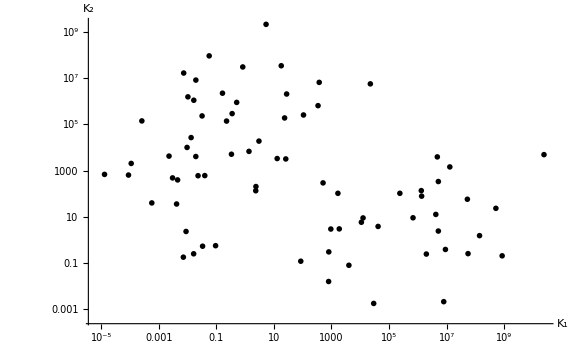

```mathematica
biPlot=ListLogLogPlot[Transpose[{biParK1,biParK2}],ImageSize->Large,PlotRange->All,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->{Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}], Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}]},TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Monochrome"]
```

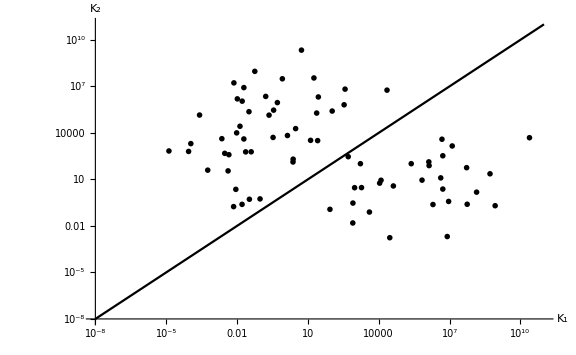

```mathematica
Show[LogLogPlot[x,{x,10^(-9),10^12},PlotRange->{{10^(-8),10^11},{10^(-8),10^11}},ImageSize->Large,PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->{Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}], Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}]},TicksStyle->Directive["Label", 14],AxesStyle-> Thick],biPlot]
```

```mathematica
Length[bistableKs]
```

11985

```mathematica
transposedKs=Transpose[bistableKs];parK1=(transposedKs[[1]]*transposedKs[[10]])/(transposedKs[[2]]*transposedKs[[11]]);parK2=(transposedKs[[4]]*transposedKs[[8]])/(transposedKs[[5]]*transposedKs[[9]]);
```

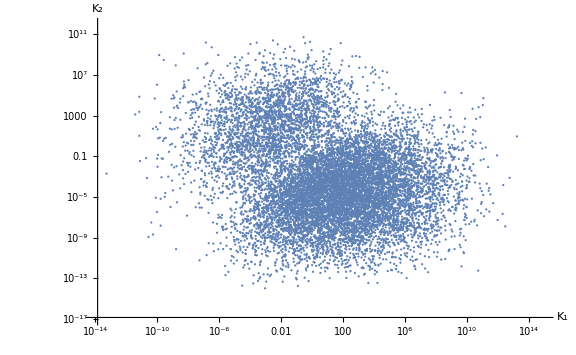

```mathematica
plot=ListLogLogPlot[Transpose[{parK1,parK2}],AxesLabel->{"K_1","K_2"},ImageSize->Large,PlotRange->{{10^(-14),10^15},{10^(-17),10^12}},LabelStyle->{32,GrayLevel[0]},AxesStyle-> Thick,Ticks->Automatic,TicksStyle->Directive["Label", 20]]
```

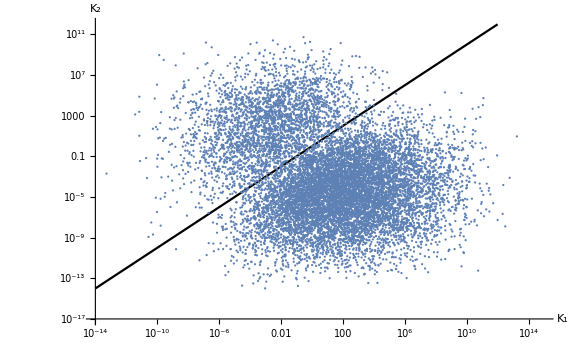

```mathematica
Show[LogLogPlot[x,{x,10^(-14),10^15},PlotRange->{{10^(-14),10^15},{10^(-17),10^12}},ImageSize->Large,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->Automatic(*{Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}], Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}]}*),TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Monochrome"],plot]
```